```mathematica
Task1[δδ_, ΔΔ_, ℵℵ_]:=Module[{δ=δδ, Δ=ΔΔ, ℵ=ℵℵ},
kvec = RandomReal[{δ, Δ}, 3]; (*Иметь возможность фиксировать kvec*)
k=Norm[kvec];
Bsin[x_]:={0, Sin[k*x[[1]]],  Cos[k*x[[1]]]} ;
Bcos[x_]:={0, Cos[k*x[[1]]],  -Sin[k*x[[1]]]} ;
ϕ = RandomReal[{0, 2π}];
Bsincos[x_]:=Cos[ϕ]*Bcos[x]+Sin[ϕ]*Bsin[x];
B[x_]:=k^ℵ Bsincos[x];
By[x_]:=B[x][[2]];
Bz[x_]:=B[x][[3]];
χ[r_]:=(By[{0,0,0}] * Bz[r* {1, 0, 0}])/(4π r^2);
χ
];
```

```mathematica
EvaluateMean[χχ_, rr_, nn_:10]:=Module[{χ=χχ,r=rr,n=nn},
Table[χ[r], {i, 0, n}] // Median
];
```

```mathematica
δ = 1/1000; Δ = 1000; ℵ=1/2;n=1000;
```

```mathematica
data =Table[EvaluateMean[Task1[δ, Δ, ℵ], r], {r, 1, 10000, 1}]
```

{-0.0881803,-0.0143073,0.00683938,0.0143007,0.0112126,-0.00549608,0.00241771,0.00144298,0.000234953,0.00100372,0.00198419,9978,5.64198×10^-10,-4.14102×10^-10,-2.79934×10^-9,-2.08593×10^-9,1.83752×10^-10,1.53334×10^-9,1.44285×10^-9,-1.26757×10^-9,1.57334×10^-9,2.6784×10^-9,7.15143×10^-10}
 |  |  |  |

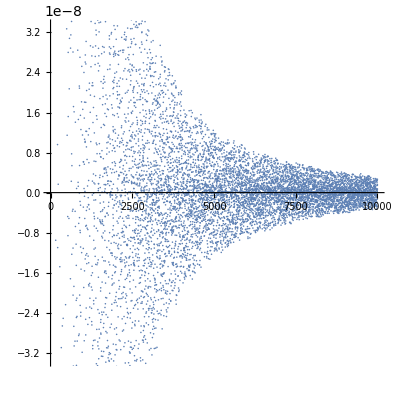

```mathematica
ListPlot[data, AspectRatio->1]
```

```mathematica
EvaluateMean[Task1[δ, Δ, ℵ], 1, 100]
```

```mathematica
δ = 1/1000; Δ = 1000; ℵ=1/10;n=1000;
```

```mathematica
data = Table[EvaluateMean[Task1[δ, Δ, ℵ], r], {r, 1000, 10000, 1}]
```

{2.02952×10^-7,-2.27931×10^-7,-2.99254×10^-7,4.47322×10^-8,-1.98701×10^-7,-1.96718×10^-7,-2.50923×10^-7,5.37055×10^-9,-2.90982×10^-7,-2.78747×10^-7,1.4763×10^-7,8979,-3.18065×10^-9,-1.62561×10^-9,3.07272×10^-9,-5.92485×10^-11,3.03546×10^-10,-9.42493×10^-10,2.43851×10^-9,-1.09253×10^-9,2.99881×10^-10,-1.74089×10^-9,-1.83537×10^-9}
 |  |  |  |

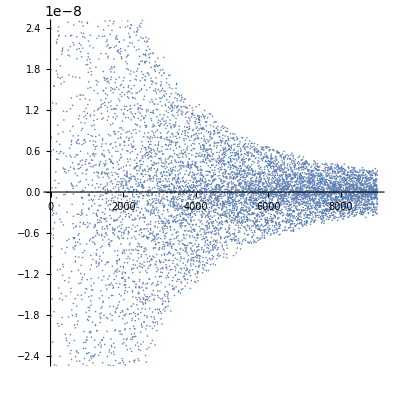

```mathematica
ListPlot[data, AspectRatio->1]
```

```mathematica
δ = 1/1000; Δ = 1000; ℵ=1.5;n=1000;
```

```mathematica
data = Table[EvaluateMean[Task1[δ, Δ, ℵ], r], {r, 1000, 10000, 1}]
```

{-0.879335,4.19073,40.5587,-46.4772,0.458863,36.224,-2.12507,0.00150722,0.00565848,-7.36345,-48.0517,0.0173711,8977,0.326271,-0.0244494,0.611239,-0.150473,0.236361,-0.0645947,-0.131161,0.371706,0.149526,2.14202,0.285509,0.0604754}
 |  |  |  |

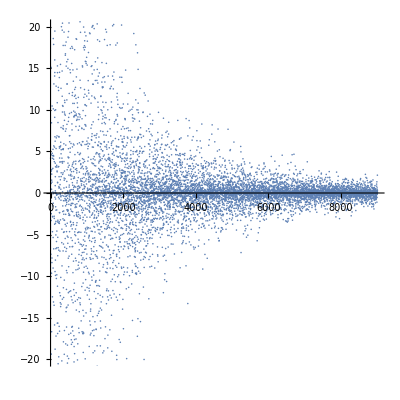

```mathematica
ListPlot[data, AspectRatio->1, PlotRange->{Automatic,{-20, 20}}]
```